## Setup

```mathematica
afinesdir="/home/simonfreedman/Code/cytomod/";
trajdir="/project/weare-dinner/simonfreedman/cytomod/out/design/trajs/";
figdir="/project/weare-dinner/simonfreedman/cytomod/out/design/figs_v2/";
```

```mathematica
Import[afinesdir<>"/analysis/cytomod_functions.m"];
```

```mathematica
nf1[x_]:=NumberForm[x,{2,1}];
nf2[x_]:=NumberForm[x,{2,2}];

importsum[f_]:=With[{dat=importCheck[f]},{Total[dat],Length[dat]}];

intv[vac_,ti_:1,tf_:-1]:=Total[0.5(vac[[(ti+1);;tf,2]]+vac[[ti;;(tf-1),2]])(vac[[(ti+1);;tf,1]]-vac[[ti;;(tf-1),1]])];
gt[x_,y_]:=If[x>y,1,0];


ClearAll[intmeangrb,intmeangr,meshavg];
intmeangr[dir_,ti_:1,tf_:50,maxr_:100,file_:grf]:=With[{grdat=importCheck[dir<>file]},
If[Dimensions[grdat][[2]]==1,intv[Mean[grdat[[ti;;tf,1,1;;maxr]]]],intv[Mean[grdat[[ti;;tf,1;;maxr]]]]]
];
intmeangrb[dir_,ti_:1,tf_:50,maxr_:100,grf_:grf, grbf_:grbf]:=intv@With[
{grdat=importCheck[dir<>grf],grbdat=importCheck[dir<>grbf]},
If[Dimensions[grdat][[2]]==1,
{grbdat[[ti,1,2;;maxr,1]],Mean[grbdat[[ti;;tf,1,2;;maxr,2]]]/Mean[grdat[[ti;;tf,1,2;;maxr,2]]]}ᵀ,
{grbdat[[1,2;;maxr,1]],Mean[grbdat[[ti;;tf,2;;maxr,2]]]/Mean[grdat[[ti;;tf,2;;maxr,2]]]}ᵀ,
]
];
meshavg[dir_,meshsizef_:meshsizef]:=Mean[Flatten[importCheck[dir<>meshsizef]]];
```

```mathematica
intmeangrbdats[grdat_,grbdat_,ti_:1,tf_:50,maxr_:100]:=intv@
If[Dimensions[grdat][[2]]==1,
{grbdat[[ti,1,2;;maxr,1]],Mean[grbdat[[ti;;tf,1,2;;maxr,2]]]/Mean[grdat[[ti;;tf,1,2;;maxr,2]]]}ᵀ,
{grbdat[[1,2;;maxr,1]],Mean[grbdat[[ti;;tf,2;;maxr,2]]]/Mean[grdat[[ti;;tf,2;;maxr,2]]]}ᵀ,
];
```

```mathematica
seedMdensXldens=
Table[StringJoin[ToString/@{trajdir,"dens_dens_ka5/seed",sd,"e7_mdens",nf2@md,"_xldens",nf1@xd}],
{sd,1,5},
{md,{0,0.01,0.02,0.05,0.1,0.2,0.3}},
{xd,{0,0.1,0.2,0.5,0.8,1,1.2,1.5}}
];
```

```mathematica
seedMkoffXlkoff=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len10_mkoff",nf2@mk,"_xlkoff",nf2@xlk}],
{sd,1,5},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}},
{xlk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenMkoff=
Table[StringJoin[ToString/@{trajdir,"mkoff_len/seed",sd,"e7_len",len,"_mkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenXlkoff=
Table[StringJoin[ToString/@{trajdir,"xlkoff_len/seed",sd,"e7_len",len,"_xlkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenMkoffXlkoff20=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len",len,"_mkoff",nf2@mk,"_xlkoff0.05"}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenXlkoffMkoff5=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len",len,"_mkoff0.20_xlkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];


forestgreen=RGBColor[34/255,139/255,34/255];
```

```mathematica
(*bpscsd1=Flatten@seedMdensXldens[[1,{1,-1},{1,-1}]];
bpscsds=Flatten/@seedMdensXldens[[All,{1,-1},{1,-1}]];*)
```

## Order parameter calculations

These calculations are potentially slow, so its best to do them on the different trajectories in parallel, if you have access to mathematica command line, using listed scripts, as described in README.md

### g (r)

### g(r_barb)

### mesh size

### msd

### angle distribution

## Phase Portraits (Figs. 1, S1, 3,S5, S6,S7 6A)

### 1

```mathematica
phasespace=Flatten@seedMdensXldens[[1,{1,4,7},{1,5,8}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[-1]],{dr,phasespace}];
ams=ParallelTable[pts2[dr,"amotors"][[-1]],{dr,phasespace}];
pms=ParallelTable[pts2[dr,"pmotors"][[-1]],{dr,phasespace}];
```

```mathematica
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],3]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
ddphases
```

```mathematica
Export[figdir<>"/f1.eps",ddphases];
```

### S1

```mathematica
frs=Table[draw[{},{lks[[i]]},
If[Dimensions[ams[[i]]][[2]]==8,{ams[[i,1;;-1;;1]]},{}],
If[Dimensions[pms[[i]]][[2]]==8,{pms[[i,1;;-1;;1]]},{}],
"",False,{50,50},True,11],{i,Length[ams]}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],3]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
ddphases
```

```mathematica
Export[figdir<>"/fs1.eps",ddphases];
```

### 3

```mathematica
(*dir=phasespace[[3]];*)
dir=outdir<>"/structs/dens_dens/mkoff0.1_mkend0.1/sd1e7/mdens0.00_xldens1.5";
ac=pts2[dir,"actins"][[-1,All,1;;2]];
```

```mathematica
np=500;
nm=11;
nsb=10;
fov={50,50};
acallb=Table[mysubdivide[ac[[j*nm+i]],ac[[j nm+i+1]],nsb,fov],{j,0,np-1},{i,1,nm-1}];
acplt=ListPlot[Flatten[acallb,2],Joined->False,PlotStyle->Red,PlotMarkers->{●,5},PlotRange->25{{-1,1},{-1,1}},FrameTicks->None,AspectRatio->1,Axes->None];
```

```mathematica
thresh=1;
vxsz=0.25;
nbxs=fov[[1]]/vxsz;
bncnts=BinCounts[Flatten[acallb,2],{-0.5fov[[1]],0.5fov[[2]],vxsz},{-0.5fov[[1]],0.5fov[[2]],vxsz}];
bc=Map[If[#>=thresh,1,0]&,bncnts,{2}];
```

```mathematica
sp0s=Table[SequencePosition[bc[[All,t]],{Repeated[0]},Overlaps->False],{t,Length[bc]}];
d=ConstantArray[0,{200,200}];
Do[d[[i,z[[1]];;z[[2]]]]=z[[2]]-z[[1]],{i,Length[sp0s]},{z,sp0s[[i]]}];

sp0sCol=Table[SequencePosition[bc[[t]],{Repeated[0]},Overlaps->False],{t,Length[bc]}];
dCol=ConstantArray[0,{200,200}];
Do[dCol[[i,z[[1]];;z[[2]]]]=z[[2]]-z[[1]],{i,Length[sp0sCol]},{z,sp0sCol[[i]]}];

dat=0.25/2Reverse@(dColᵀ+d);
```

```mathematica
(*cf=ColorData[{"SunsetColors","Reversed"}];
plt=Show[ArrayPlot[Log10@(dat+0.125),ColorFunction->cf,ColorFunctionScaling->True],
ArrayPlot[Reverse@Transpose@bc,ColorFunction->(If[#>0,Black,Transparent]&)]
];
leg=logbarleg[Min[dat+0.125],Max[dat+0.125],4,cf,NumberForm[#-0.125,{2,1}]&,{LegendMarkerSize->{30,300},LabelStyle->Directive[Black,FontSize->22],LegendLabel->Placed[Rotate["mesh size (μm)",3Pi/2],Right]}]*)
```

```mathematica
cf=ColorData[{"BlueGreenYellow",{Max[dat],Min[dat]}}];
plt=Show[ArrayPlot[dat,ColorFunction->cf,ColorFunctionScaling->False],
ArrayPlot[Reverse@Transpose@bc,ColorFunction->(If[#>0,White,Transparent]&)]
]
```

```mathematica
leg=BarLegend[{cf,{Min[dat],Max[dat]}},LegendMarkerSize->{30,300},LabelStyle->Directive[Black,FontSize->22],LegendLabel->Placed[Rotate["mesh size (μm)",3Pi/2],Right]]
```

```mathematica
Export[figdir<>"/3bgy.svg",plt];
Export[figdir<>"/3bgy_leg.svg",leg];
```

### S5

```mathematica
phasespace=Flatten@seedMkoffXlkoff[[2,{1,3,5,7},{1,3,5,7}]];
```

```mathematica
lks=Table[pts2[dr,"links"][[400]],{dr,phasespace}];
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Transpose@Reverse@Partition[frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"motor lifetime (s)","crosslinker lifetime (s)"},FrameTicks->{
{{{-1250,1},{-900,5},{-550,20},{-200,100}},None},
{{{200,1},{550,5},{900,20},{1250,100}},None}},FrameStyle->Directive[FontSize->30,Black]];;
```

```mathematica
Export[figdir<>"/S5.pdf",phases]; (*use font size of 16 for pdfs instead of 30*)
```

```mathematica
Export[figdir<>"/S5.pdf",phases];
```

```mathematica
Export[figdir<>"/S6.png",phases,ImageSize->{1000,1000}];
```

### S6

```mathematica
phasespace=Flatten@seedLenMkoff[[2,{1,4,5,6},{1,4,5,7}]];
```

```mathematica
lks=Table[pts2[dr,"links"][[400]],{dr,phasespace}];
frs=Table[drawmixed[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Partition[Reverse@frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"motor lifetime (s)","filament length (μm)"},FrameTicks->{
{{{-1250,1},{-900,8},{-550,10},{-200,15}},None},
{{{200,1},{550,5},{900,10},{1250,100}},None}},FrameStyle->Directive[FontSize->30,Black]];
```

```mathematica
Export[figdir<>"/S6.png",phases,ImageSize->{1000,1000}];
```

```mathematica
Export[figdir<>"/S6.pdf",phases];
Export[figdir<>"/S6.png",phases];
```

### S7

```mathematica
phasespace=Flatten@seedLenXlkoff[[2,{1,3,4,6},{1,3,4,7}]];
```

```mathematica
lks=Table[pts2[dr,"links"][[400]],{dr,phasespace}];
```

```mathematica
frs=Table[drawmixedpolar[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Partition[Reverse@frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"crosslinker lifetime (s)","filament length (μm)"},FrameTicks->{
{{{-1250,1},{-900,5},{-550,8},{-200,15}},None},
{{{200,1},{550,10},{900,20},{1250,100}},None}},FrameStyle->Directive[FontSize->30,Black]];
```

```mathematica
Export[figdir<>"/S7.png",phases,ImageSize->{1000,1000}];
```

```mathematica
phases
```

```mathematica
Export[figdir<>"/fs7.eps",phases];
```

### 6A

```mathematica
phasespace=Flatten@seedMdensXldens[[1,{1,7},{1,8}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[-1]],{dr,phasespace}];
```

```mathematica
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],2]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/S10C_lks.eps",ddphases];
```

```mathematica
myline[xy_,col_,thickness_,max_:10]:=If[Norm[xy[[1]]-xy[[2]]]≤max,{col,Thickness[thickness],Line[xy]},Nothing];
```

#### colored by trajectory

```mathematica
(*amots=pts2[#<>"/restart_more_motors_long_kend10/seed1e6","amotors"]&/@phasespace;*)
amots=pts2[#<>"/motor_walk_dynamic_mkend0.1/seed1e6","amotors"]&/@phasespace;
```

```mathematica
amotcms=amots[[All,1;;-1;;10,1;;10,1;;2]]+0.5amots[[All,1;;-1;;10,1;;10,3;;4]];
amotsnr=Map[Split[#][[All,1]]&,Transpose/@amotcms,{2}];
```

```mathematica
Dimensions[amotsnr]
```

{4,10,200,2}

```mathematica
pr={{-25,25},{-25,25}};
nc=4;
sz=0.75;
cf=ColorData[{"BlueGreenYellow",{1,nc}}];
ti=1;
tf=200;
```

```mathematica
ixs=RandomSample[1;;10,nc];
ls=Table[myline[amotsnr[[j,i,t;;(t+1)]],cf[i],0.005],{j,4},{i,1,nc},{t,tf-ti-1}];
spts=Table[{EdgeForm[{Thick,cf[i]}],FaceForm[White],Disk[amotsnr[[j,i,1]],sz]},{j,4},{i,nc}];
epts=Table[{EdgeForm[{Thick,cf[i]}],FaceForm[White],Rectangle[amotsnr[[j,i,tf]]-sz,amotsnr[[j,i,tf]]+sz]},{j,4},{i,nc}];
```

```mathematica
frms=Table[Graphics[Join[ls[[i]],spts[[i]],epts[[i]]],PlotRange->pr],{i,Length[ls]}];
trajs=GraphicsGrid[Reverse@(Partition[frms,2]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
trajs
```

```mathematica
Export[figdir<>"/trajs_4_mots.eps",trajs];
```

#### colored by time

```mathematica
ti=1;tf=1650;
```

```mathematica
cf=ColorData[{"BlueGreenYellow",{1,tf-ti}}];

ls=Table[myline[amotcms[[i,t;;(t+1)]],cf[t],0.005],{i,Length[amotcms]},{t,tf-ti-1}];
```

```mathematica
frms=Table[Graphics[ls[[i]],PlotRange->{{-25,25},{-25,25}}],{i,Length[ls]}];
trajs=GraphicsGrid[Reverse@(Partition[frms,2]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/S10C_mots.eps",trajs];
```

## Structural Consequences (Figs 2, 6B-C, 7A-B, S2, S7)

### plotting settings

```mathematica
bpscdirs=Transpose@(Flatten/@seedMdensXldens[[All,{1,-1},{1,-1}]]);

th=0.012;
th2=0.008;
pss={Directive[Black,Thickness[th2]],Directive[Lighter@Blue,Thickness[th]],Directive[forestgreen,Thickness[th]],Directive[Red,Thickness[th]]};
leg=PointLegend[{"homogenous","bundled","polarity sorted","contracted"},Spacings->0,LabelStyle->FontSize->22,LegendMarkerSize->20];
```

### 2 A

Preprocessing : requires gr script to be run on bpscdirs (last 50 s only)

```mathematica
grf="/analysis/gr_dr0.05_maxr25t351-400.dat";
grdats=Map[importCheck[#<>grf][[All,1]]&,bpscdirs,{2}];
mugrs=Table[{gr[[1,All,1]]+0.025,Mean[gr[[All,All,2]]]}ᵀ,{gr,Flatten[#,1]&/@grdats}];
```

```mathematica
p1=ListPlot[mugrs,
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,11.8},{0,31.5}},
FrameLabel->{"actin-actin distance (μm)","radial distribution"},
Joined->True];
```

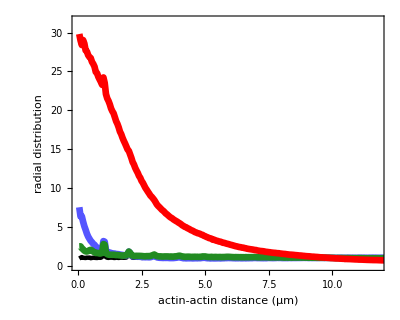

```mathematica
p1
```

```mathematica
Export[figdir<>"/2A.svg",p1];
```

```mathematica
p2=ListPlot[mugrs[[All,1;;]],
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,2.5},{0.5,7.7}},
FrameTicks->{{LinTicks[-1,8,2,10],Automatic},{LinTicks[0,3,1,10],Automatic}},
Joined->True,
BaseStyle->FontSize->36];
```

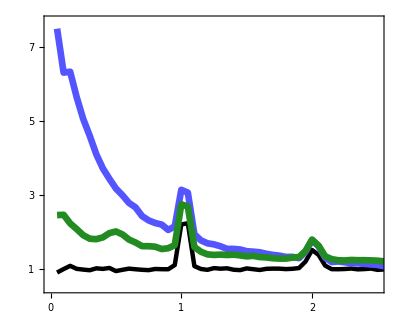

```mathematica
p2
```

```mathematica
Export[figdir<>"/2Ainset.svg",p2];
```

### 2 B

Preprocessing : requires gr_barbed and gr script to be run on bpscdir (last 50 s only)

```mathematica
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
grbdats=Map[importCheck[#<>grbf][[All,1]]&,bpscdirs,{2}];
```

```mathematica
grdatsf=Flatten[#,1]&/@grdats;
grbdatsf=Flatten[#,1]&/@grbdats;
mugrbs=Table[{grbdatsf[[i,1,All,1]]+0.025,Mean[grbdatsf[[i,All,All,2]]]/Mean[grdatsf[[i,All,All,2]]]}ᵀ,{i,Length[grbdatsf]}];
```

```mathematica
p1=ListPlot[mugrbs,
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,2.65},{0,57}},
FrameLabel->{"barb-barb distance (μm)","radial distr. (norm)"},
Axes->{False,True},AxesOrigin->{0.5,0},AxesStyle->Directive[Black,Thickness[0.007],Dashed],
PlotLegends->Placed[leg,{0.65,0.7}]
];
```

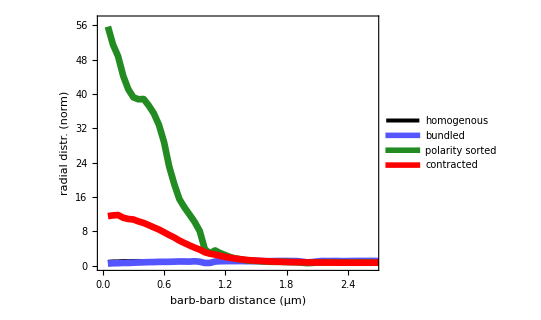

```mathematica
p1
```

```mathematica
Export[figdir<>"/2B.svg",p1];
```

### 2 C

Preprocessing : requires mesh size and gr script to be run on bpscdirs (whole trajectory)

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";
dats=Map[importCheck[#<>meshsizef][[All,1]]&,bpscdirs,{2}];
```

```mathematica
maxr=48;
minr=0;
dr=0.25;
bcs=Table[BinCounts[Flatten[dats[[i]]],{minr,maxr,dr}],{i,Length[dats]}];
probs=bcs/(dr*Total/@bcs);
```

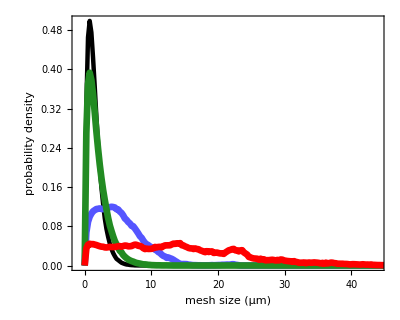

```mathematica
plt=ListPlot[probs,DataRange->{minr,maxr},
PlotRange->{{-1,44},Full},
PlotMarkers->None,
PlotStyle->pss,
FrameLabel->{"mesh size (μm)","probability density"},PlotRange->Full]
```

```mathematica
Export[figdir<>"/2C.svg",plt];
```

```mathematica
meshsizefullf="/analysis/meshsizes_1D_vx0.25_thresh1_t1-400.dat";
msdatsfull=Map[(Mean[Flatten[#]]&)/@importCheck[#<>meshsizefullf]&,bpscdirs,{2}];
```

```mathematica
rmax=10;
dr=0.05;
grfullf="/analysis/gr_dr0.05_maxr25t1-400.dat";
grints=Map[((intv[#,1,Round[rmax/dr]]/rmax&)/@(importCheck[#<>grfullf][[All,1]]))&,bpscdirs,{2}];
```

```mathematica
mspltdat=msdatsfull/grints;
```

```mathematica
plt=ListPlot[Mean/@mspltdat,
PlotMarkers->None,
PlotStyle->pss,
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{Full,{1.3,4.7}},
FrameTicks->{{Table[If[MemberQ[{1.,2.,3.,4.,5.,6.},i],{i,ToString@integerize@i,{0.02,0}},{i,"",{0.01,0}}],{i,1,6.5,0.1}],Automatic},
{Table[If[MemberQ[{0,200,400},i],{i,ToString@i,{0.02,0}},{i,"",{0.01,0}}],{i,0,400,20}],Automatic
}},FrameStyle->Directive[Black,FontSize->28],
FrameTicksStyle->Directive[Black,FontSize->30]];
```

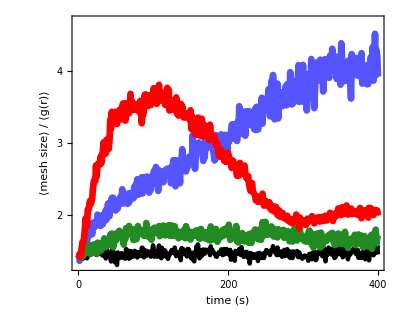

```mathematica
plt
```

```mathematica
Export[figdir<>"/2Cinset_10.svg",plt];
```

### 2D

Preprocessing : requires velocity field python script to be run, and divergence / bin count script to be run on bpscdirs

```mathematica
thresh=5;
divfname="/analysis/div_dr1_nbins10_thresh10_dt10.dat";
bcfname="/analysis/bin_counts_dr1.dat";
divthresh[dir_,thresh_]:=Module[{},
divf=importCheck[dir<>divfname];
bcf=importCheck[dir<>bcfname];
bcft=MovingAverage[0.5(bcf[[2;;]]+bcf[[;;-2]]),10];
bcfti=Map[gt[#,thresh]&,bcft,{3}];
Map[Mean[Flatten[#]]&,bcfti*divf]
];
```

```mathematica
divthreshs=Map[divthresh[#,thresh]&,bpscdirs,{2}];
```

```mathematica
tf=389;
divthavg=Mean/@divthreshs[[All,All,1;;tf]];
```

```mathematica
plt=ListPlot[MovingAverage[#,1]&/@divthavg*1000,Joined->True,PlotRange->Full,PlotMarkers->None,PlotStyle->pss,FrameLabel->{"time (s)",Style["⟨∇·v_a⟩ (10^-3s^-1)",SingleLetterItalics->False]},FrameTicks->{{Automatic,Automatic},{{#,If[Mod[#,100]==0,#,""]}&/@Range[0,400,10],Automatic}},PlotLegends->None]
```

```mathematica
Export[figdir<>"/2D.svg",plt];
```

### 6C

Preprocessing : requires angle distribution code to be run on all 77 motor trajectories from t=1001-2000 s for all bpscdirs

```mathematica
dels={1,2,5,10,20,50,100,200,500};
dth=0.01;
zval="0";
ti="1001";
```

```mathematica
motds=Table["/motor_walk_dynamic_mkend0.1/seed"<>ToString[s]<>"e6/",{s,1,77}];
angbcfs="/analysis/vmot_anghist2_t"<>ti<>"-2000d"<>ToString[#]<>"dth"<>ToString[dth]<>"_zval"<>zval<>".dat"&/@dels;
angbcs=ParallelTable[importCheck[bpscdirs[[i,j]]<>motd<>bcf],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{motd,motds},{bcf,angbcfs}];
```

```mathematica
nd=8;
angbctots=Table[Total[angbcs[[i,All,All,k,All,1]],2],{i,4},{k,nd}];
angfreqs=Table[angbctots[[i,j]]/(dth Total[angbctots[[i,j]]]),{i,1,Length[angbctots]},{j,Length[angbctots[[i]]]}];
ds=4;
angbctotsrb=Table[Total[angbctots[[i,j,k;;(k+ds-1)]]],{i,4},{j,nd},{k,1,Round[1/dth],ds}];
angfreqsrb=Table[angbctotsrb[[i,j]]/(ds*dth*Total[angbctotsrb[[i,j]]]),{i,1,Length[angbctotsrb]},{j,Length[angbctotsrb[[i]]]}];
```

```mathematica
Do[Export[outdir<>"/design/dats/dynamic_ang_hists_del"<>ToString[dels[[i]]]<>".dat",angbctots[[All,i]]],{i,Length[dels]-2}];
```

```mathematica
ft={{LinTicks[0.25,2,0.5,4],LinTicks[0.25,2,0.5,4,ShowTickLabels->False]},Automatic};
pr={{-0.01,1.01},{0.6,1.8}};
fl={"θ/2π","P(θ)"};
```

```mathematica
(*ps=Table[ListPlot[angfreqsrb[[All,i]],DataRange->{0,1},PlotRange->pr,PlotStyle->pss,PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,1,Length[angfreqsrb[[1]]]}];
Do[Export[figdir<>"7del"<>ToString[dels[[i]]*0.1]<>".svg",ps[[i]]],{i,nd}];*)
```

```mathematica
ps2=Table[ListPlot[angfreqsrb[[i,All]],DataRange->{0,1},PlotRange->pr,PlotStyle->"BlueGreenYellow",PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,Length[angfreqsrb]}];
```

```mathematica
Export[figdir<>"/7Chom.svg",ps2[[1]]];
Export[figdir<>"/7Cbun.svg",ps2[[2]]];
Export[figdir<>"/7Cps.svg",ps2[[3]]];
Export[figdir<>"/7Ccon.svg",ps2[[4]]];
```

```mathematica
leg=SwatchLegend["BlueGreenYellow",integerize/@(dels[[1;;8]]*0.1),Spacings->0,LegendLayout->"ReversedColumn",LegendMarkerSize->20,LabelStyle->FontSize->22,LegendLabel->"Δ (s)"]
```

```mathematica
Export[figdir<>"/7Cleg.pdf",leg];
```

### 6B

```mathematica
msdfs=Table["/motor_walk_dynamic_mkend0.1/seed"<>ToString[s]<>"e6/analysis/msd_t1001-2000.dat",{s,1,77}];
msds=ParallelTable[importsum[bpscdirs[[i,j]]<>f],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{f,msdfs}];
```

```mathematica
msdstots=Table[Total[msds[[i,All,All,1]],2],{i,Length[msds]}];
msdscts=Table[Total[msds[[i,All,All,2]],2],{i,Length[msds]}];
msdsmus=msdstots/msdscts;
```

```mathematica
idxs=Union@Round[10^Range[0,Log10[999],0.05]];

pr={{-1.05,2},{-1.85,2.4}};

p2=ListPlot[{Log10@(idxs/10),Log10@#[[idxs]]}ᵀ&/@(msdsmus),FrameLabel->{"Δ (s)","MSD(Δ)(μm^2)"},PlotMarkers->None,PlotStyle->pss,FrameTicks->{{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]},{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]}},PlotRange->pr,Axes->None];
p4=Show[p2,Plot[x+0.2,{x,-10,1000},PlotRange->pr,PlotStyle->{Directive[Black,Thickness[0.01],Dashed],Directive[forestgreen,Thickness[0.01],Dashed],Directive[Black,Thickness[0.01],Dashed]}]];
```

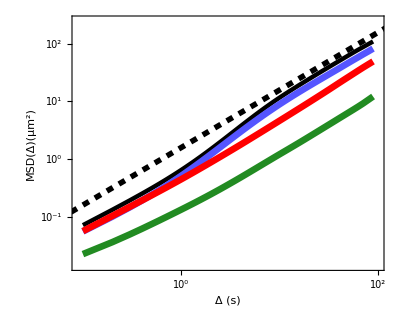

```mathematica
p4
```

```mathematica
Export[figdir<>"/7B.svg",p4];
```

### 8B

```mathematica
shearf="/shear_kxl1_kl5_dt1e-5_nframes50000/data/pe.txt";
(*shearf="/shear_kl1000_kxl100/data/pe.txt";*)
```

```mathematica
bpscdirsext=Table[outdir<>"/design/trajs/dens_dens_ka5/seed"<>ToString[i]<>"e7_mdens0.30_xldens1.5",{i,6,10}];
bpscdirs2=Join[bpscdirs[[1;;3]],{Join[bpscdirs[[4]],bpscdirsext]}];
```

```mathematica
te=Map[Total[Transpose[importCheck[#<>shearf]]]&,bpscdirs,{2}];
```

```mathematica
(*de=Map[(#-#[[1]])&,te,{2}];
teavg=Map[MovingAverage[#,50]&,te,{2}];*)
```

```mathematica
(*tf=Min[Flatten[Map[Length,teavg,{2}]]];*)
len=50000;
ndps=100;
tf=0.5;
teavg=Map[Mean/@Partition[#,len/ndps]&,te,{2}];
idxs=Range[1,ndps];
eqengs=Mean/@(teavg[[All,All,idxs]]);
vol=50*50*0.1(*μm^3*);
dW=eqengs-eqengs[[All,1]];
dw=dW/vol;
γs=tf/ndps idxs ;
dats=({γs,#}ᵀ)&/@dw;
```

```mathematica
leg
```

PointLegend[{homogenous,bundled,polarity sorted,contracted},Spacings→0,LabelStyle→FontSize→22,LegendMarkerSize→20]

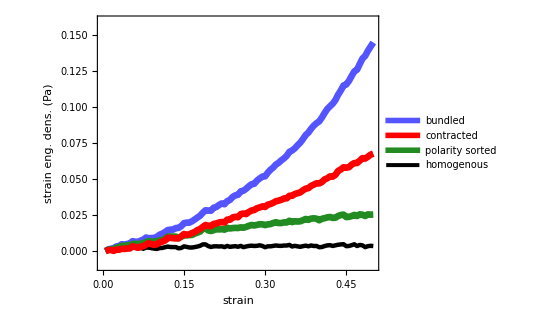

```mathematica
leg2=LineLegend[pss[[{2,4,3,1}]],{"bundled","contracted","polarity sorted","homogenous"},Spacings->0,LabelStyle->FontSize->22,LegendMarkerSize->20];
plt=ListPlot[dats,PlotRange->{Automatic,{-0.01,0.16}},PlotStyle->pss,PlotMarkers->None,PlotLegends->Placed[leg2,{0.37,0.75}],FrameLabel->{"strain","strain eng. dens. (Pa)"},BaseStyle->FontSize->20]
```

```mathematica
Export[figdir<>"/8B.svg",plt];
```

#### bpsc shear moduli

```mathematica
ti=1;
gs=Map[1/2D[Fit[#[[ti;;]],{1,x,x^2},x],{x,2}]&,dats,{1}];
```

```mathematica
gquadfits=Map[LinearModelFit[#[[ti;;]],x^2,x]&,dats,{1}];
glinfits=Map[LinearModelFit[#[[ti;;]],x,x]&,dats,{1}];
gboth=Map[LinearModelFit[#[[ti;;]],{1,x,x^2},x]&,dats,{1}];
gpower=Map[NonlinearModelFit[#[[ti;;]],x^a,{a},x]&,dats,{1}];
```

```mathematica
Normal/@gboth//TableForm
```

0.00100583+0.014431 x-0.0185863 x^2
0.0040306+0.00703753 x+0.536306 x^2
0.000247536+0.0801264 x-0.0598746 x^2
-0.0012704+0.0626234 x+0.151864 x^2

```mathematica
#["RSquared"]&/@gquadfits-(#["RSquared"]&/@glinfits)
```

{-0.128727,0.0582747,-0.131018,0.00676453}

```mathematica
#["RSquared"]&/@gquadfits
```

{0.333725,0.998109,0.833403,0.98506}

```mathematica
#["RSquared"]&/@glinfits
```

{0.462452,0.939834,0.964421,0.978296}

```mathematica
gsti=Table[Map[1/2D[Fit[#[[ti;;]],{1,x,x^2},x],{x,2}]&,dats,{1}],{ti,1,800}];
```

```mathematica
gquads=Table[Map[1/2D[Fit[#[[ti;;]],{x^2},x],{x,2}]&,dats,{1}],{ti,1,800}];
glins=Table[Map[1/2D[Fit[#[[ti;;]],{x},x],x]&,dats,{1}],{ti,1,800}];
```

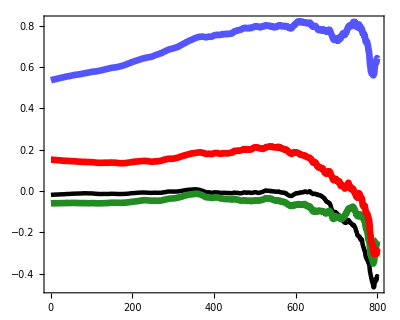

```mathematica
ListPlot[gstiᵀ,PlotMarkers->None,PlotStyle->pss]
```

#### log log version

```mathematica
idxs=Union@Round[10^Range[0,Log10[50000],0.05]];
eqengs=Mean/@(te[[All,All,idxs]]);
dW=eqengs-eqengs[[All,1]];
dw=dW/vol;
γs=0.00001idxs ;
dats=({γs,#}ᵀ)&/@dw;
```

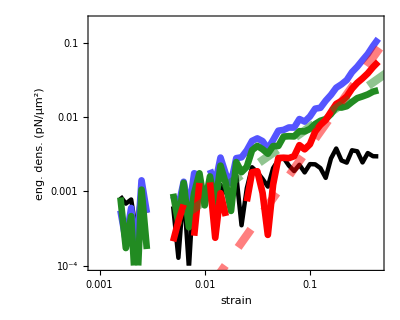

```mathematica
p2=
Show[
ListLogLogPlot[dats,PlotRange->{Automatic,{0.0001,0.2}},PlotRange->{Automatic,{0.00001,0.2}},PlotStyle->pss,PlotMarkers->None,FrameLabel->{"strain","eng. dens. (pN/μm^2)"},BaseStyle->FontSize->19],
Plot[{x-2.6,2x-0.9},{x,-5,3},PlotStyle->{{forestgreen,Dashing[0.04],Thickness[0.015],Opacity[0.5]},{Red,Dashing[0.04],Thickness[0.015],Opacity[0.5]}}]]
```

```mathematica
Export[figdir<>"/8Bll.svg",p2];
```

### 8A

```mathematica
lks=pts2[bpscdirs[[2,1]]<>"/shear_kxl1_kl5_dt1e-5","links"];
```

```mathematica
(*engs=(Norm/@Flatten[lks[[All,All,3;;4]],1]-1);*)
engs=Map[Norm[#]-1&,lks[[{201,501,-1},All,3;;4]],{2}];
englims={-0.01,0.01};
```

```mathematica
fov={50,50};
englims={0.1,-0.01};
fs0=drawStretch[{},{lks[[201]]},{},{},"",False,fov,1,Red,{0,0},0.1,1,True,englims,"ThermometerColors"];
fs1=drawStretch[{},{lks[[501]]},{},{},"",False,fov,1,Red,{0,0},0.25,1,True,englims,"ThermometerColors"];
fs2=drawStretch[{},{lks[[-1]]},{},{},"",False,fov,1,Red,{0,0},0.5,1,True,englims,"ThermometerColors"];
{fs0,fs1,fs2}
```

```mathematica
Export[figdir<>"/8Atop_therm.pdf",Show[fs0]];
Export[figdir<>"/8Amid_therm.pdf",Show[fs1]];
Export[figdir<>"/8Abot_therm.pdf",Show[fs2]];
```

```mathematica
drawStretch[{},lks[[1;;-1;;10]],{},{},bpscdirs[[2,1]]<>"/restart_shear",True,fov,1,Red,{0,0},0.1,1,True,englims,"ThermometerColors"];
```

```mathematica
bpscdirs[[2,1]]
```

/project/weare-dinner/simonfreedman/cytomod/out/design/trajs/dens_dens_ka5/seed1e7_mdens0.00_xldens1.5

```mathematica
Manipulate[Show[lks[[t]]],{t,1,Length[lks],10}]
```

### S2A

```mathematica
dr=0.05;
grfullf="/analysis/gr_dr0.05_maxr25t351-400.dat";
```

```mathematica
grs=Map[importCheck[#<>grfullf][[All,1]]&,bpscdirs,{2}];
```

```mathematica
rmaxs=Join[{0.05,0.25,0.5},Range[1,25]];
```

```mathematica
grints=Table[intv[grs[[i,j,t]],1,Round[rmax/dr]]/rmax,{i,Length[grs]},{j,Length[grs[[i]]]},{t,Length[grs[[i,j]]]},{rmax,rmaxs}];
```

```mathematica
grintsmu=Table[Mean[Flatten@grints[[i,All,All,r]]],{i,4},{r,28}];
```

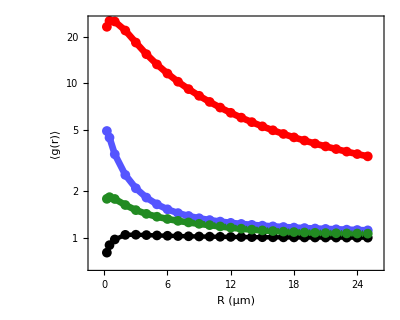

```mathematica
plt=ListLogPlot[{rmaxs[[2;;]],#}ᵀ&/@grintsmu[[All,2;;]],
PlotRange->{{-1,26},Full},
PlotMarkers->{●,10},
PlotStyle->pss,
FrameLabel->{"R (μm)","⟨g(r)⟩"},PlotRange->Full]
```

```mathematica
Export[figdir<>"/S2A.svg",plt];
```

### S2B

```mathematica
dr=0.05;
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
```

```mathematica
grbs=Map[importCheck[#<>grbf][[All,1]]&,bpscdirs,{2}];
```

```mathematica
grbints=Table[intv[grbs[[i,j,t]],1,Round[rmax/dr]]/rmax,{i,Length[grbs]},{j,Length[grbs[[i]]]},{t,Length[grbs[[i,j]]]},{rmax,rmaxs}];
```

```mathematica
grbintsmu=Table[Mean[Flatten@(grbints[[i,All,All,r]])],{i,4},{r,28}];
```

```mathematica
grbintsmu=Table[Mean[Flatten[grbints[[i,All,All,r]]/grints[[i,All,All,r]]]],{i,4},{r,2,28}];
```

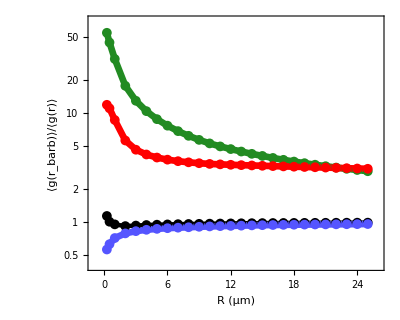

```mathematica
plt=ListLogPlot[{rmaxs[[2;;]],#}ᵀ&/@grbintsmu,
PlotRange->{{-1,26},{0.4,70}},
PlotMarkers->{●,10},
PlotStyle->pss,
FrameLabel->{"R (μm)","⟨g(r_barb)⟩/⟨g(r)⟩"},PlotRange->Full]
```

```mathematica
Export[figdir<>"/S2B.svg",plt];
```

### S2C

```mathematica
meshsizefullf="/analysis/meshsizes_1D_vx0.25_thresh1_t1-400.dat";
msdatsfull=Map[(Mean[Flatten[#]]&)/@importCheck[#<>meshsizefullf]&,bpscdirs,{2}];
```

```mathematica
grintsfull=Table[intv[grs[[i,j,t]],1,Round[rmax/dr]]/rmax,{i,4},{j,3},{t,1,400},{rmax,rmaxs}];
```

```mathematica
mspltdatrmax=Table[msdatsfull/grintsfull[[All,All,All,r]],{r,4,Length[rmaxs]}];
```

```mathematica
msdpltrmaxmu=Map[Mean,mspltdatrmax,{2}];
```

```mathematica
idxs={1,2,5,10,15,20,25};
```

```mathematica
p1=ListPlot[msdpltrmaxmu[[idxs,1]],
PlotMarkers->None,
PlotStyle->"BlueGreenYellow",
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{0.8,3.8},
PlotLegends->SwatchLegend[rmaxs[[idxs+3]],LegendLabel->"r_max(μm)",LegendMarkerSize->20,Spacings->0]
]
```

```mathematica
p2=ListPlot[msdpltrmaxmu[[idxs,2]],
PlotMarkers->None,
PlotStyle->"BlueGreenYellow",
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{0.9,5.2},
PlotLegends->SwatchLegend[rmaxs[[idxs+3]],LegendLabel->"r_max(μm)",LegendMarkerSize->20,Spacings->0]
]
```

```mathematica
Export[figdir<>"/meshsize_gr_rmax_bun.svg",p2];
```

```mathematica
p3=ListPlot[msdpltrmaxmu[[idxs,3]],
PlotMarkers->None,
PlotStyle->"BlueGreenYellow",
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{0.7,2.7},
PlotLegends->SwatchLegend[rmaxs[[idxs+3]],LegendLabel->"r_max(μm)",LegendMarkerSize->20,Spacings->0]
]
```

```mathematica
Export[figdir<>"/meshsize_gr_rmax_ps.svg",p3];
```

```mathematica
p4=ListPlot[msdpltrmaxmu[[idxs,4]],
PlotMarkers->None,
PlotStyle->"BlueGreenYellow",
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{0.4,6.3},
PlotLegends->SwatchLegend[rmaxs[[idxs+3]],LegendLabel->"r_max(μm)",LegendMarkerSize->20,Spacings->0]
]
```

```mathematica
Export[figdir<>"/meshsize_gr_rmax_con.svg",p4];
```

```mathematica
ps=Table[ListPlot[msdpltrmaxmu[[idxs,i]],
PlotMarkers->None,
PlotStyle->"BlueGreenYellow",
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{0.4,6.3},
PlotLegends->SwatchLegend[rmaxs[[idxs+3]],LegendLabel->Placed["R (μm)",Below],LegendMarkerSize->20,Spacings->0,LabelStyle->FontSize->22,LegendLayout->table]
],{i,4}];
```

```mathematica
table[pairs_]:=TableForm[Transpose@pairs,TableAlignments->Center,TableSpacing->{0.1,0.5}];
```

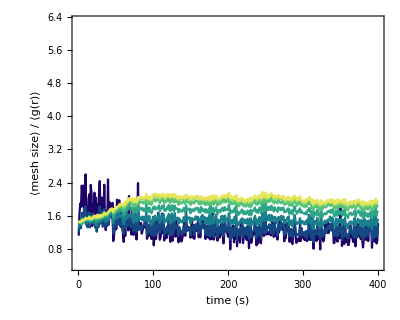

```mathematica
ps[[3]]
```

```mathematica
Do[Export[figdir<>"/meshsize_gr_R_"<>ToString[i]<>".svg",ps[[i]]],{i,4}];
```

```mathematica
msgrrmaxtfmu=Table[Mean[Flatten[msdatsfull[[i,All,351;;]]/grintsfull[[i,All,351;;,r]]]],{i,4},{r,4,Length[rmaxs]}];
```

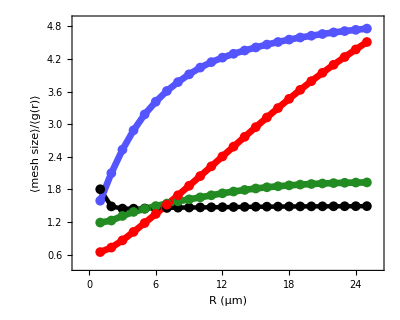

```mathematica
plt=ListPlot[{rmaxs[[4;;]],#}ᵀ&/@(msgrrmaxtfmu),
PlotRange->{{-1,26},{0.4,4.9}},
PlotMarkers->{●,10},
PlotStyle->pss,
FrameLabel->{"R (μm)","⟨mesh size⟩/⟨g(r)⟩"},PlotRange->Full]
```

```mathematica
Export[figdir<>"/bpsc_meshsize_gr_R.svg",plt];
```

## Phase Diagrams (Fig. 4, 7C-F)

### plotting settings

```mathematica
allopts={ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{Full,Full,Full},BaseStyle->FontSize->20};
st[f_,idxs_]:=Table[If[MemberQ[idxs,i],ToString[f[[i]]],""],{i,Range[Length[f]]}];

mds={0,0.01,0.02,0.05,0.1,0.2,0.3};
mdsp=mds;mdsp[[1]]=0.005;
xlds={0,0.1,0.2,0.5,0.8,1,1.2,1.5};
xlidxs=Join[{1},Range[3,Length[xlds]]];
midxs=Range[2,Length[mds]-1];
fts={
{{xlds,st[xlds,xlidxs]}ᵀ,{xlds,ConstantArray["",Length[xlds]]}ᵀ},{Join[{{Log10[0.005],"0"}},{Log10@mds,st[mds,midxs]}ᵀ[[2;;]]],{Join[{Log10[0.005]},Log10@mds[[2;;]]],ConstantArray["",Length[mds]]}ᵀ}};
densopts=Join[allopts,{FrameTicks->fts,FrameLabel->{"motor density (μm^-2)","crosslinker density (μm^-2)"}}];

kidxs=Range[7];
ks={0.01,0.02,0.05,0.1,0.2,0.5,1};
ksinv=1/ks;
logks=Log10@ksinv;
fts={
{{logks,st[ksinv,kidxs]}ᵀ,{logks,ConstantArray["",Length[ksinv]]}ᵀ},
{{logks,st[ksinv,kidxs]}ᵀ,{logks,ConstantArray["",Length[ksinv]]}ᵀ}
};

koffopts=Join[allopts,{FrameTicks->fts,FrameLabel->{"motor lifetime (s)","crosslinker lifetime (s)"}}];
```

### A , D

```mathematica
dr=0.05;
maxr=10;
ti=-50;
tf=-1;
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grintsdd=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,seedMdensXldens,{3}];
grintsddmu=Mean@grintsdd;
```

```mathematica
MinMax[Log10[grintsddmu]]
```

{0.00961383,0.879171}

```mathematica
pr={0,0.88};
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@grintsddmu[[i,j]]},{i,Length[grintsddmu]},{j,Length[grintsddmu[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

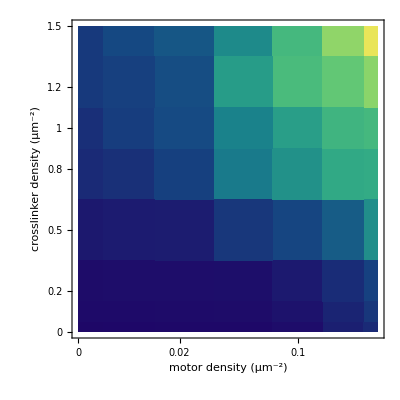

```mathematica
p1
```

```mathematica
Export[figdir<>"/4A.svg",p1];
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grintskk=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,seedMkoffXlkoff,{3}];
grintskkmu=Mean@grintskk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10[ksinv[[j]]],Log10@grintskkmu[[i,j]]},{i,Length[ksinv]},{j,Length[ksinv]}],1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

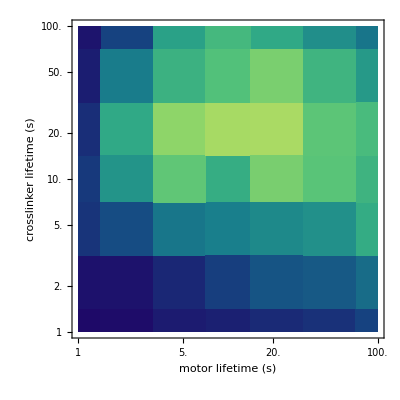

```mathematica
p2
```

```mathematica
leg=logbarleg[10^pr[[1]],10^pr[[2]],5,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨g(r)⟩",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
Export[figdir<>"/4A_10.svg",p1];
Export[figdir<>"/4D_10.svg",p2];
Export[figdir<>"/4ADleg_10.pdf",leg];
```

### B, E

```mathematica
dr=0.05;
maxr=10;
ti=-50;
tf=-1;
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbf="/analysis/gr_barbed_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbintsdd=Map[intmeangrb[#,ti,tf,Round[maxr/dr],grf,grbf]/maxr&,dddirs,{3}];
grbintsddmu=Mean@grbintsdd;
```

```mathematica
MinMax[Log10@grbintsddmu]
```

{-0.0248059,0.511361}

```mathematica
pr={0,0.52};
leg=logbarleg[10^pr[[1]],10.^pr[[2]],5,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨g(r_barb)/g(r)⟩",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@grbintsddmu[[i,j]]},{i,Length[grbintsddmu]},{j,Length[grbintsddmu[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

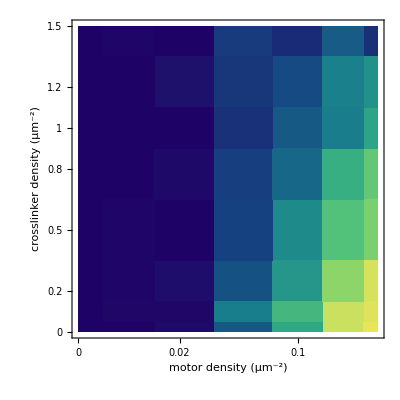

```mathematica
p1
```

```mathematica
Export[figdir<>"/4B_"<>ToString[maxr]<>".svg",p1];
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbf="/analysis/gr_barbed_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbintskk=Map[intmeangrb[#,ti,tf,Round[maxr/dr],grf,grbf]/maxr&,seedMkoffXlkoff,{3}];
grbintskkmu=Mean@grbintskk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10[ksinv[[j]]],Log10@grbintskkmu[[i,j]]},{i,Length[ksinv]},{j,Length[ksinv]}],1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

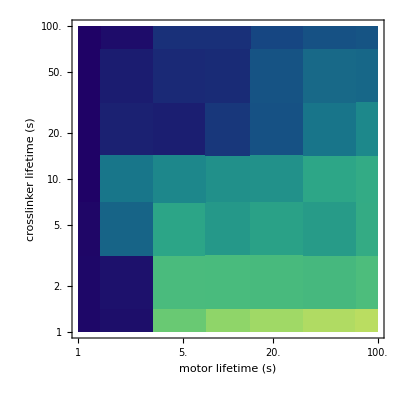

```mathematica
p2
```

```mathematica
Export[figdir<>"/4E_"<>ToString@maxr<>".svg",p2];
Export[figdir<>"/4BEleg_"<>ToString@maxr<>".svg",leg];
```

### C, F

```mathematica
pr={0.16,0.66};
leg=logbarleg[10^pr[[1]],10^pr[[2]],4,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨mesh size⟩/⟨g(r)⟩ (μm)",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";
mszdd=Map[meshavg[#,meshsizef]&,dddirs,{3}];
```

```mathematica
Export[outdir<>"/design/dats/densdens_mesh.dat",mszdd];
```

```mathematica
mszdd=importCheck[outdir<>"/design/dats/densdens_mesh.dat"];
```

```mathematica
mszgrdd=mszdd/grintsdd; (*get grintsdd from A,D above*)
mszgrddmu=Mean@mszgrdd;
```

```mathematica
pr={0.16,0.66};
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@mszgrddmu[[i,j]]},{i,Length[mdsp]},{j,Length[xlds]}] ,1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

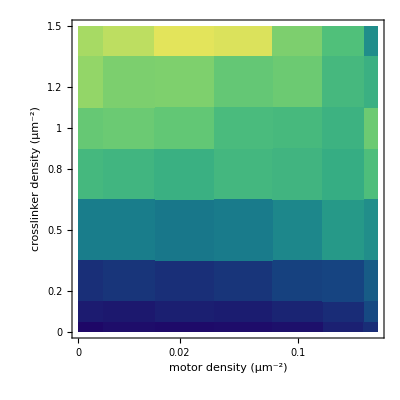

```mathematica
p1
```

```mathematica
Export[outdir<>"/design/dats/densdens_mesh_gr.dat",mszgrddmu];
```

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";
mszkk=Map[meshavg[#,meshsizef]&,seedMkoffXlkoff,{3}];
```

```mathematica
Export[outdir<>"/design/dats/koffkoff_mesh.dat",mszkk];
```

```mathematica
mszgrkk=mszkk/grintskk; (*get grintsdd from A,D above*)
mszgrkkmu=Mean@mszgrkk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10@ksinv[[j]],Log10@mszgrkkmu[[i,j]]},{i,Length[ks]},{j,Length[ks]}] ,1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

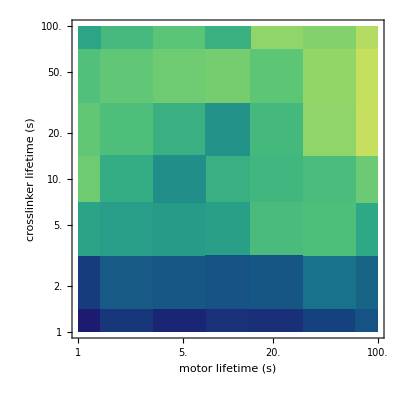

```mathematica
p2
```

```mathematica
Export[figdir<>"/4C_"<>ToString[maxr]<>".svg",p1];
Export[figdir<>"/4F_"<>ToString@maxr<>".svg",p2];
```

```mathematica
Export[figdir<>"/4CFleg_"<>ToString[maxr]<>".svg",leg];
```

```mathematica
Export[outdir<>"/design/dats/koffkoff_mesh_gr.dat",mszgrkkmu];
```

### 7C-F

#### dens dens

```mathematica
shearf="/shear_kxl1_kl5_dt1e-5_dd/data/pe.txt";
te=Map[Total[Transpose[importCheck[#<>shearf]]]&,seedMdensXldens,{3}];
```

```mathematica
idx0=1;
tf=0.5;
ndps=1000;
vol=50*50*0.1(*μm^3*);
ti=1;

eqengs=Mean@te;
dW=eqengs-eqengs[[All,All,1]];
dw=dW/vol;
γs=tf/ndps Range[ndps] ;
dats=Map[({γs,#}ᵀ)&,dw,{2}];
(*gs=Map[1/2D[Fit[#[[ti;;]],{1,x,x^2},x],{x,2}]&,dats,{2}];*)
```

```mathematica
gboth=Map[LinearModelFit[#[[ti;;]],{1,x,x^2},x]&,dats,{2}];
gs1=Map[D[Normal[#],{x,2}]&,gboth,{2}];
etas1=Map[(D[Normal[#],x]/.{x->0})&,gboth,{2}];
```

```mathematica
prG=Log10@{0.048,2.8};
leg=logbarleg[10^prG[[1]],10^prG[[2]],5,"BlueGreenYellow",NumberForm[#,{4,2}]&,{LegendLabel->Placed[Rotate["shear modulus (Pa)",3Pi/2],Right],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Right}]
```

```mathematica
thresh[x_,th_:-1]:=If[Im[x]≠0||x<th,th,x];
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],thresh[Log10@gs1[[i,j]],prG[[1]]]},{i,Length[gs1]},{j,Length[gs1[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",prG}]];
```

```mathematica
p1
```

```mathematica
leg=BarLegend[{"BlueGreenYellow",pr},(*NumberForm[#,{4,1}]&,*)LegendLabel->Placed[Rotate["shear modulus (Pa)",3Pi/2],Right],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Right]
```

```mathematica
Export[figdir<>"/dens_dens_G_prG.svg",p1];
Export[figdir<>"/prG_leg.svg",leg];
```

```mathematica
prE={0,0.092};
d2=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],etas1[[i,j]]},{i,Length[etas1]},{j,Length[etas1[[i]]]}],1];
p2=ListDensityPlot[d2,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",prE}]];
```

```mathematica
p2
```

```mathematica
legE=BarLegend[{"BlueGreenYellow",prE},(*NumberForm[#,{4,1}]&,*)LegendLabel->Placed[Rotate["viscosity (Pa·s)",3Pi/2],Right],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Right]
```

```mathematica
Export[figdir<>"/dens_dens_eta_prE.svg",p2];
Export[figdir<>"/prE_leg.svg",legE];
```

#### len xlkoff

```mathematica
lens={1,2,5,8,10,15};
mks={0.01,0.02,0.05,0.1,0.2,0.5,1};

ks={0.01,0.02,0.05,0.1,0.2,0.5,1};
ksinv=1/ks;
logks=Log10@ksinv;
fts={
{{lens,st[lens,Range[6]]}ᵀ,{lens,ConstantArray["",Length[lens]]}ᵀ},
{{logks,st[ksinv,kidxs]}ᵀ,{logks,ConstantArray["",Length[ksinv]]}ᵀ}

};

lenkoffopts=Join[allopts,{FrameTicks->fts,FrameLabel->{"crosslinker lifetime (s)","filament length (μm)"}}];
```

```mathematica
shearf="/shear_kxl1_kl5_dt1e-5_xl/data/pe.txt";
te=Map[Total[Transpose[importCheck[#<>shearf]]]&,seedLenXlkoff,{3}];
```

```mathematica
eqengs=Mean@te;
dW=eqengs-eqengs[[All,All,1]];
dw=dW/vol;
dats=Map[({γs[[1;;Length[#]]],#-(#[[1]])}ᵀ)&,dw,{2}];
```

```mathematica
gboth=Map[LinearModelFit[#[[ti;;]],{1,x,x^2},x]&,dats,{2}];
gs2=Map[D[Normal[#],{x,2}]&,gboth,{2}];
etas2=Map[(D[Normal[#],x]/.{x->0})&,gboth,{2}];
```

```mathematica
prG
```

{-1.31876,0.447158}

```mathematica
MinMax
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],thresh[Log10@gs1[[i,j]],prG[[1]]]},{i,Length[gs1]},{j,Length[gs1[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",prG}]];
```

```mathematica
(*pr={0,2.8};*)
d1=Flatten[Table[{Log10[ksinv[[j]]],lens[[i]],thresh[Log10@gs2[[i,j]],prG[[1]]]},{i,Length[gs2]},{j,Length[gs2[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@lenkoffopts,ColorFunction->ColorData[{"BlueGreenYellow",prG}]];
```

```mathematica
p1
```

```mathematica
leg=BarLegend[{"BlueGreenYellow",pr},(*NumberForm[#,{4,1}]&,*)LegendLabel->Placed[Rotate["shear modulus (Pa)",3Pi/2],Right],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Right]
```

```mathematica
Export[figdir<>"/xlkoff_len_G_prG.svg",p1];
(*Export[figdir<>"/xlkoff_len_G_leg.svg",leg];*)
```

```mathematica
(*pr={0,0.0673};*)
d2=Flatten[Table[{Log10[ksinv[[j]]],lens[[i]],etas2[[i,j]]},{i,Length[etas2]},{j,Length[etas2[[i]]]}],1];
p2=ListDensityPlot[d2,Evaluate@lenkoffopts,ColorFunction->ColorData[{"BlueGreenYellow",prE}]];
```

```mathematica
p2
```

```mathematica
leg=BarLegend[{"BlueGreenYellow",pr},(*NumberForm[#,{4,1}]&,*)LegendLabel->Placed[Rotate["viscosity (Pa·s)",3Pi/2],Right],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Right]
```

```mathematica
Export[figdir<>"/xlkoff_len_eta_prE.svg",p2];
(*Export[figdir<>"/xlkoff_len_eta_leg.svg",leg];*)
```

### koff koff with errors

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grintskk=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,seedMkoffXlkoff,{3}];
```

```mathematica
(*Plot Options*)
idxs={1,4,7};
nc=Length[idxs];
cf=ColorData["BlueGreenYellow"];
cols=Flatten[Table[cf/@ConstantArray[i,3],{i,0,1,1.0/(nc-1)}]];
joind=Flatten[ConstantArray[{True,False,False},nc]];
pms=Flatten[Table[errbarpms[cf[i],Rectangle[]],{i,0,1,1.0/(nc-1)}],1];
fills=Flatten[Table[{i->{i+1}},{i,2,3*nc,3}],1];

koffs={0.01,0.02,0.05,0.1,0.2,0.5,1};
tixx={Log10[1/#],ToString[1/#]}&/@koffs;
tixxn={Log10[1/#],""}&/@koffs;
ftix={Automatic,{Join[tixx[[1;;-1;;2]],tixxn],tixxn}};

koffleg=SwatchLegend[cols[[1;;-1;;3]],integerize/@Reverse@ksinv[[idxs]],LegendLabel->Text[Style["motor\nlifetime (s)", LineSpacing->{0,20},TextAlignment->Left]],Spacings->0,LegendMarkerSize->15,LegendLayout->"Column"];
```

```mathematica
grintskkmu=Mean@grintskk;
grintskkerr=StandardDeviation[grintskk]/Sqrt[Length[grintskk]];
cs=Table[errcurves[Log10[ksinv],grintskkmu[[i]],grintskkerr[[i]]],{i,idxs}];
```

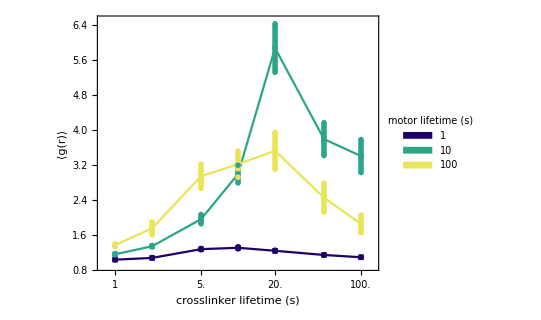

```mathematica
pr={{-0.1,2.1},{0.9,6.5}};
p1=ListPlot[Flatten[Reverse@Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[Opacity[1],Thickness[0.01]],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨g(r)⟩"},PlotLegends->Placed[koffleg,{0.25,0.7}]]
```

```mathematica
Export[figdir<>"/4D_gr_errs.eps",p1];
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbf="/analysis/gr_barbed_dr"<>ToString[dr]<>"_maxr25t351-400.dat";
grbintskk=Map[intmeangrb[#,ti,tf,Round[maxr/dr],grf,grbf]/maxr&,seedMkoffXlkoff,{3}];
```

```mathematica
grbintskkmu=Mean@grbintskk;
grbintskkerr=StandardDeviation[grbintskk]/Sqrt[Length[grbintskk]];
csb=Table[errcurves[Log10[ksinv],grbintskkmu[[i]],grintskkerr[[i]]],{i,idxs}];
```

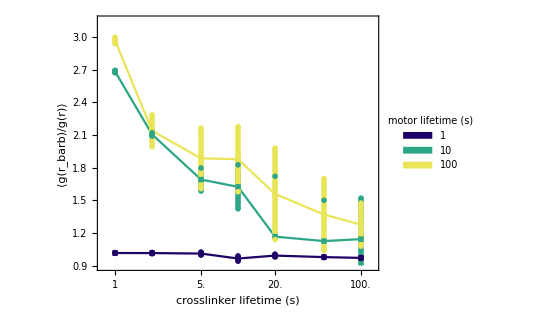

```mathematica
pr={{-0.1,2.1},{0.9,3.15}};
p2=ListPlot[Flatten[Reverse@Map[Reverse,csb,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[Opacity[1],Thickness[0.01]],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨g(r_barb)/g(r)⟩"},PlotLegends->Placed[koffleg,{0.77,0.7}]]
```

```mathematica
Export[figdir<>"/4E_errs.eps",p2];
```

```mathematica
mszkk=importCheck[outdir<>"/design/dats/koffkoff_mesh.dat"];
```

```mathematica
mszgrkk=mszkk/grintskk; (*get grintsdd from A,D above*)
mszgrkkmu=Mean@mszgrkk;
mszgrkkerr=StandardDeviation[mszgrkk]/Sqrt[Length[mszgrkk]];
csm=Table[errcurves[Log10[ksinv],mszgrkkmu[[i]],mszgrkkerr[[i]]],{i,idxs}];
```

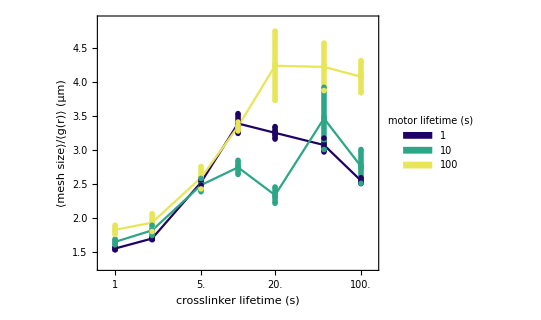

```mathematica
pr={{-0.1,2.1},{1.3,4.9}};
p3=ListPlot[Flatten[Reverse@Map[Reverse,csm,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[Opacity[1],Thickness[0.01]],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨mesh size⟩/⟨g(r)⟩ (μm)"},PlotLegends->Placed[koffleg,{0.25,0.7}]]
```

```mathematica
Export[figdir<>"/4F_errs.eps",p3];
```

## Koff / Length (Figs. 5, S3)

### plot setup

```mathematica
grf="/analysis/gr_dr0.05_maxr25t351-400.dat";
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";

(*Plot Options*)
cf=ColorData["BlueGreenYellow"];
cols=Flatten[Table[cf/@ConstantArray[i,3],{i,0,1,0.2}]];
joind=Flatten[ConstantArray[{True,False,False},6]];
pms=Flatten[Table[errbarpms[cf[i],Rectangle[]],{i,0,1,0.2}],1];
fills=Flatten[Table[{i->{i+1}},{i,2,18,3}],1];


koffs={0.01,0.02,0.05,0.1,0.2,0.5,1};
lens={1,2,5,8,10,15};
seeds={2,3,4,5};
tixx={Log10[1/#],ToString[1/#]}&/@koffs;
tixxn={Log10[1/#],""}&/@koffs;
ftix={Automatic,{Join[tixx[[1;;-1;;2]],tixxn],tixxn}};

idx[i_]:=Min[Max[4/i,1],350];
idxs[i_]:=With[{start=idx[koffs[[Mod[i-1,10]+1]]]},Range[start,start+50]];

dr=0.05;
maxr=25;
ti=-50;
tf=-1;
```

### 5A

```mathematica
pkdirs=seedLenXlkoffMkoff5;
mkdirs=seedLenMkoffXlkoff20;
```

```mathematica
pkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,seedLenXlkoffMkoff5,{3}];
```

```mathematica
pkgrsmu=Mean[pkgrs];
pkgrserr=StandardDeviation[pkgrs]/Sqrt[Length[pkgrs]];
cs=Table[errcurves[Log10[1/koffs],pkgrsmu[[i]],pkgrserr[[i]]],{i,Length[pkgrsmu]}];
```

```mathematica
mkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,seedLenMkoffXlkoff20,{3}];
```

```mathematica
mkgrsmu=Mean[mkgrs];
mkgrserr=StandardDeviation[mkgrs]/Sqrt[Length[mkgrs]];
csmk=Table[errcurves[Log10[1/koffs],mkgrsmu[[i]],mkgrserr[[i]]],{i,Length[mkgrsmu]}];
```

```mathematica
pkc400=cs[[5]];
mkc400=csmk[[5]];
```

```mathematica
pkdirs10=pkdirs[[All,5]];
mkdirs10=mkdirs[[All,5]];
```

```mathematica
grf="/analysis/gr_dr0.05_maxr25t1-400.dat";
```

```mathematica
mkgr=Map[importCheck[#<>grf]&,mkdirs10,{2}];
pkgr=Map[importCheck[#<>grf]&,pkdirs10,{2}];
```

```mathematica
mks400=intmeangr[#,351,400,100,grf]&/@mkdirs10[[All,1]];
```

```mathematica
mkgrstfk=Table[intv[Mean[mkgr[[s,i,idxs[i],1,1;;Round[maxr/dr]]]]],{s,Length[mkgr]},{i,Length[mkgr[[s]]]}];
mkgrtfkmu=Mean[mkgrstfk/maxr];
mkgrtfkerr=StandardDeviation[mkgrstfk/maxr]/Sqrt[Length[mkgrstfk]];
mkctfk=errcurves[Log10[1/koffs],mkgrtfkmu,mkgrtfkerr];
```

```mathematica
pkgrstfk=Table[intv[Mean[pkgr[[s,i,idxs[i],1,1;;Round[maxr/dr]]]]],{s,Length[pkgr]},{i,Length[pkgr[[s]]]}];
pkgrtfkmu=Mean[pkgrstfk/maxr];
pkgrtfkerr=StandardDeviation[pkgrstfk/maxr]/Sqrt[Length[pkgrstfk]];
pkctfk=errcurves[Log10[1/koffs],pkgrtfkmu,pkgrtfkerr];
```

```mathematica
lenleg=SwatchLegend[cols[[1;;-1;;3]],lens,LegendLabel->Text[Style["         filament\n         length (μm)", LineSpacing->{0,20},TextAlignment->Left]],Spacings->0,LegendMarkerSize->15,LegendLayout->"ReversedColumn"];
```

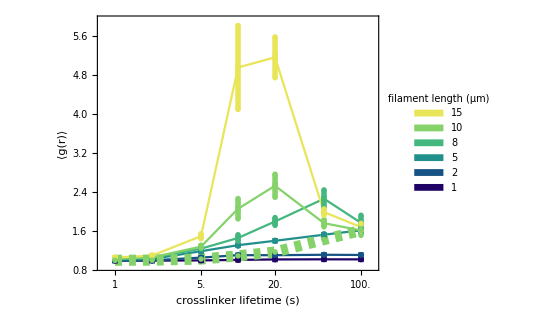

```mathematica
pr={{-0.1,2.1},{0.9,5.9}};
p1=ListPlot[Join[Flatten[Map[Reverse,cs,{2}],1],{Reverse@pkctfk[[1]]}],PlotStyle->Join[cols,{Directive[cols[[5*3]],Thickness[0.02],CapForm["Butt"],Dashed]}],Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[Opacity[1],Thickness[0.01]],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨g(r)⟩"},PlotLegends->Placed[lenleg,{0.15,0.5}]]
```

```mathematica
Export[figdir<>"/5Aright_25.svg",p1];
```

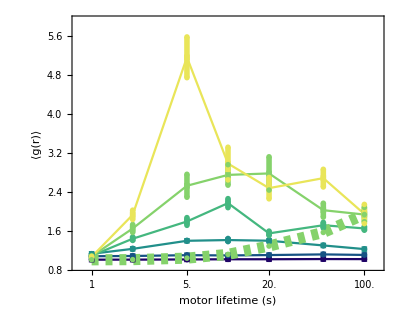

```mathematica
p2=ListPlot[Join[Flatten[Map[Reverse,csmk,{2}],1],{Reverse[mkctfk[[1]]]}],PlotStyle->Join[cols,{Directive[Thickness[0.02],cols[[5*3]],CapForm["Butt"],Dashed]}],Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"motor lifetime (s)","⟨g(r)⟩"}]
```

```mathematica
Export[figdir<>"/5Aleft_25.svg",p2];
```

### S3 A

```mathematica
dirs=seedLenMkoff;
```

```mathematica
mkgrbs=Map[intmeangrb[#,ti,tf,Round[maxr/dr]]/maxr&,dirs,{3}];
```

```mathematica
mkgrbsmu=Mean[mkgrbs];
mkgrbserr=StandardDeviation[mkgrbs]/Sqrt[Length[mkgrbs]];
cs=Table[errcurves[Log10[1/koffs],mkgrbsmu[[i]],mkgrbserr[[i]]],{i,Length[mkgrbsmu]}];
```

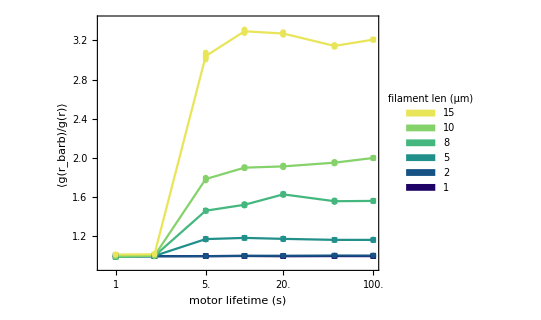

```mathematica
pr={{-0.1,2},{0.9,3.4}};
lenleg=SwatchLegend[cols[[1;;-1;;3]],lens,LegendLabel->Text[Style["      filament\n      len (μm)", LineSpacing->{0,20},TextAlignment->Left]],Spacings->0,LegendMarkerSize->15,LegendLayout->"ReversedColumn"];
p1=ListPlot[Flatten[Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"motor lifetime (s)","⟨g(r_barb)/g(r)⟩"},PlotLegends->Placed[lenleg,{0.1,0.55}]]
```

```mathematica
Export[figdir<>"/S3A.svg",p1];
```

### 5 B

```mathematica
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
mkgrbbs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grbf]/maxr&,dirs,{3}];
```

```mathematica
mkgrbsmu=Mean[mkgrbbs];
mkgrbserr=StandardDeviation[mkgrbbs]/Sqrt[Length[mkgrbbs]];
cs=Table[errcurves[Log10[1/koffs],mkgrbsmu[[i]],mkgrbserr[[i]]],{i,Length[mkgrbsmu]}];
```

```mathematica
dirs10=dirs[[All,5]];
```

```mathematica
(*c1=cs[[5]];
*)
```

```mathematica
grbf="/analysis/gr_barbed_dr0.05_maxr25t1-400.dat";
grbs=Map[importCheck[#<>grbf]&,dirs10,{2}];
```

```mathematica
grbstfk=Table[intmeangr[dirs10[[s,i]],idxs[i][[1]],idxs[i][[-1]],Round[maxr/dr],grbf]/maxr,{s,Length[dirs10]},{i,Length[dirs10[[s]]]}];
```

```mathematica
(*grbstfk=Table[intv[Mean[grbs[[s,i,idxs[i],1,1;;maxr/dr]]]]/maxr,{s,Length[grbs]},{i,Length[grbs[[s]]]}];*)
grbstfkmu=Mean[grbstfk];
grbstfkerr=StandardDeviation[grbstfk]/Sqrt[Length[grbstfk]];
c2=errcurves[Log10[1/koffs],grbstfkmu,grbstfkerr];
```

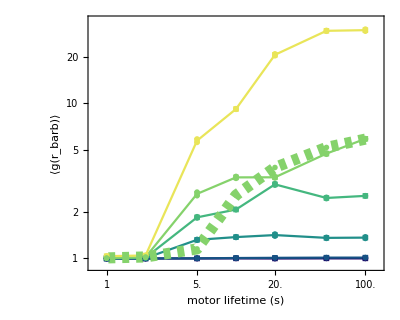

```mathematica
p1=ListLogPlot[Join[Flatten[cs,1],{c2[[1]]}],PlotStyle->Join[cols,{Directive[cols[[5*3]],Thickness[0.02],CapForm["Butt"],Dashed]}],Joined->joind,PlotMarkers->Join[pms,{Null}],FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->{{-0.1,2.1},{0.9,34}},FrameTicks->ftix,FrameLabel->{"motor lifetime (s)","⟨g(r_barb)⟩"}]
```

```mathematica
Export[figdir<>"/5B_25.svg",p1];
```

### S3B

```mathematica
dirs=seedLenXlkoff;
```

```mathematica
maxr
```

25

```mathematica
grf="/analysis/gr_dr0.05_maxr25t351-400.dat";
xlkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,dirs,{3}];
```

```mathematica
xlkmesh=Map[meshavg[#,meshsizef]&,dirs,{3}];
```

```mathematica
xlkmgr=xlkmesh/(xlkgrs);
xlkmgrmu=Mean[xlkmgr];
xlkmgrerr=StandardDeviation[xlkmgr]/Sqrt[Length[xlkmgr]];
cs=Table[errcurves[Log10[1/koffs],xlkmgrmu[[i]],xlkmgrerr[[i]]],{i,Length[xlkmgrmu]}];
```

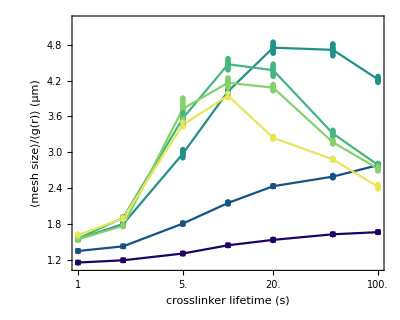

```mathematica
p1=ListPlot[Flatten[Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[Opacity[1],Thickness[0.01]],
Filling->fills,PlotRange->{Full,{1.1,5.2}},FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨mesh size⟩/⟨g(r)⟩ (μm)"}]
```

```mathematica
Export[figdir<>"/S3B.svg",p1];
```

### 5 C

```mathematica
xlkmmu=Mean[xlkmesh];
xlkmerr=StandardDeviation[xlkmesh]/Sqrt[Length[xlkmesh]];
cs=Table[errcurves[Log10[1/koffs],xlkmmu[[i]],xlkmerr[[i]]],{i,Length[xlkmmu]}];
```

```mathematica
Export[outdir<>"/design/dats/5C_squares_rmax25.dat",cs];
```

```mathematica
cs=importCheck[outdir<>"/design/dats/5C_squares_rmax25.dat"];
```

```mathematica
dirs10=dirs[[All,5]];
meshsizef2="/analysis/meshsizes_1D_vx0.25_thresh1_t1-400.dat";
xlkmeshk=Table[Mean[Flatten[importCheck[dirs10[[s,i]]<>meshsizef2][[idxs[i]]]]],{s,Length[dirs10]},{i,Length[dirs10[[s]]]}];
```

```mathematica
xlkmeshkmu=Mean[xlkmeshk];
xlkmeshkerr=StandardDeviation[xlkmeshk]/Sqrt[Length[xlkmeshk]];
meshcurvesk=errcurves[Log10[1/koffs],xlkmeshkmu,xlkmeshkerr];
```

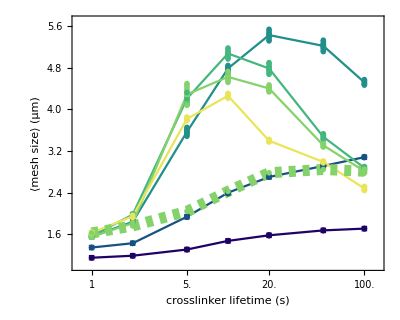

```mathematica
p1=ListPlot[Join[Flatten[Map[Reverse,cs,{2}],1],{Reverse[meshcurvesk[[1]]]}],PlotStyle->Join[cols,{Directive[cols[[5*3]],Thickness[0.02],CapForm["Butt"],Dashed]}],Joined->joind,PlotMarkers->Join[pms,{Null}],PlotRange->{{-0.1,2.1},{1,5.7}},FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,FrameTicks->ftix,FrameLabel->{"crosslinker lifetime (s)","⟨mesh size⟩ (μm)"}]
```

```mathematica
Export[figdir<>"/5C_25.svg",p1];
```